# Определение микропараметров Br_2 с помощью спектрометра

## Калибровка спектрометра

Калибровку будем проводить по ртутной лампе. С помощью атласа линий ртути сопоставим линии излучения с номером пикселя.

Лабораторная справка

Img0073.nef-- for calibration
Img0074.nef-- big bottle
Img0075.nef-- big + cone bottles
Img0076.nef-- cone bottle
Img0077.nef-- small bottle
Img0078.nef-- clear lamp
Img0079.nef-- all bottles together
Img0080.nef-- cone bottle (again)
Img0081.nef-- cone bottle (high res)

```mathematica
CalibrationHg=Import["C:\\Users\\alexn\\Documents\\GitHub\\Labs\\Phys_Labs\\5_sem\\Exam lab\\Br2 Data Processing\\Hg_Calibration_Table.xlsx"][[1]][[2;;All,1;;2]];
```

```mathematica
calibWaveLengths=CalibrationHg[[All,1]]
```

{6234.37,6123.27,6072.64,5890.16,5872.03,5859.38,5803.65,5790.65,5769.59,5675.86,5460.74,5425.25,5405.79,5365.06,5045.82,5025.64,4960.32}

```mathematica
calibPixel=CalibrationHg[[All,2]]
```

{267.571,416.182,487.603,764.627,791.798,812.386,905.857,930.13,966.516,1134.56,1566.92,1642.36,1690.87,1781.86,2637.85,2700.59,2911.81}

```mathematica
calibrationHgReady=Transpose[ArrayReshape[AppendTo[calibPixel,calibWaveLengths],{2,Length[calibWaveLengths]}]];
```

Построим график зависимости длины волны от номера пикселя.

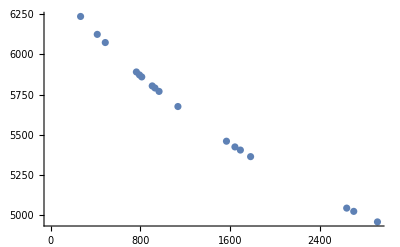

```mathematica
ListPlot[calibrationHgReady]
```

Аппроксимируем точки. Формула для калибровки имеет вид a+c/(x-b) .

```mathematica
fit=FindFit[calibrationHgReady,{a+c/(x-b),b<0},{a,b,c},x]
```

{a→2909.51,b→-3992.57,c→1.4175×10^7}

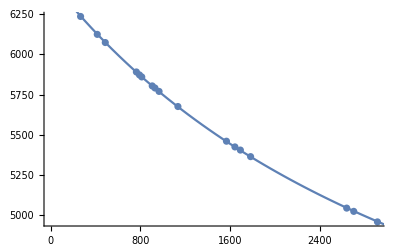

```mathematica
Show[ListPlot[calibrationHgReady],Plot[a+c/(x-b)/.fit,{x,0,3000}]]
```

Таким образом, получили функцию для калибровки :

```mathematica
Calibrate[λ_]:=a+c/(λ-b)/.fit;
```

## Выделение серий

```mathematica
i2Spectre=ReadList["C:\\Users\\alexn\\Documents\\GitHub\\Labs\\Phys_Labs\\5_sem\\Exam lab\\16_01_2019_1\\0075_clear.txt",Number,WordSeparators->{"\t", "\n"}];
```

```mathematica
i2Spectre=ArrayReshape[i2Spectre,{Length[i2Spectre]/5,5}];
```

```mathematica
len=Length[i2Spectre];
```

```mathematica
peaks={};
peaksStorage={};
```

```mathematica
Manipulate[Grid[{p,{Show[ListLinePlot[Transpose[{i2Spectre[[x;;y,1]],i2Spectre[[x;;y,Channel+1]]}],ImageSize->Large],ListLinePlot[peaks,PlotStyle->Red]]},peaks}],{{x,0,"Begin"},1,len},{{y,Length[i2Spectre],"End"},1,len},{Channel,{1,2,3,4}},

Button["Add",AppendTo[peaks,MinimalBy[Transpose[{i2Spectre[[p[[1]]*10-50;;p[[1]]*10+50,1]],i2Spectre[[p[[1]]*10-50;;p[[1]]*10+50,Channel+1]]}],Last][[1]]]],
Button["Delete last",peaks=Delete[peaks,Length[peaks]]],
Button["Clear",peaks={}],
Button["To storage",AppendTo[peaksStorage,Transpose[peaks]],peaks={}],
{{p,{0,0}},Locator},
ContentSize->{600, 460}
]
```